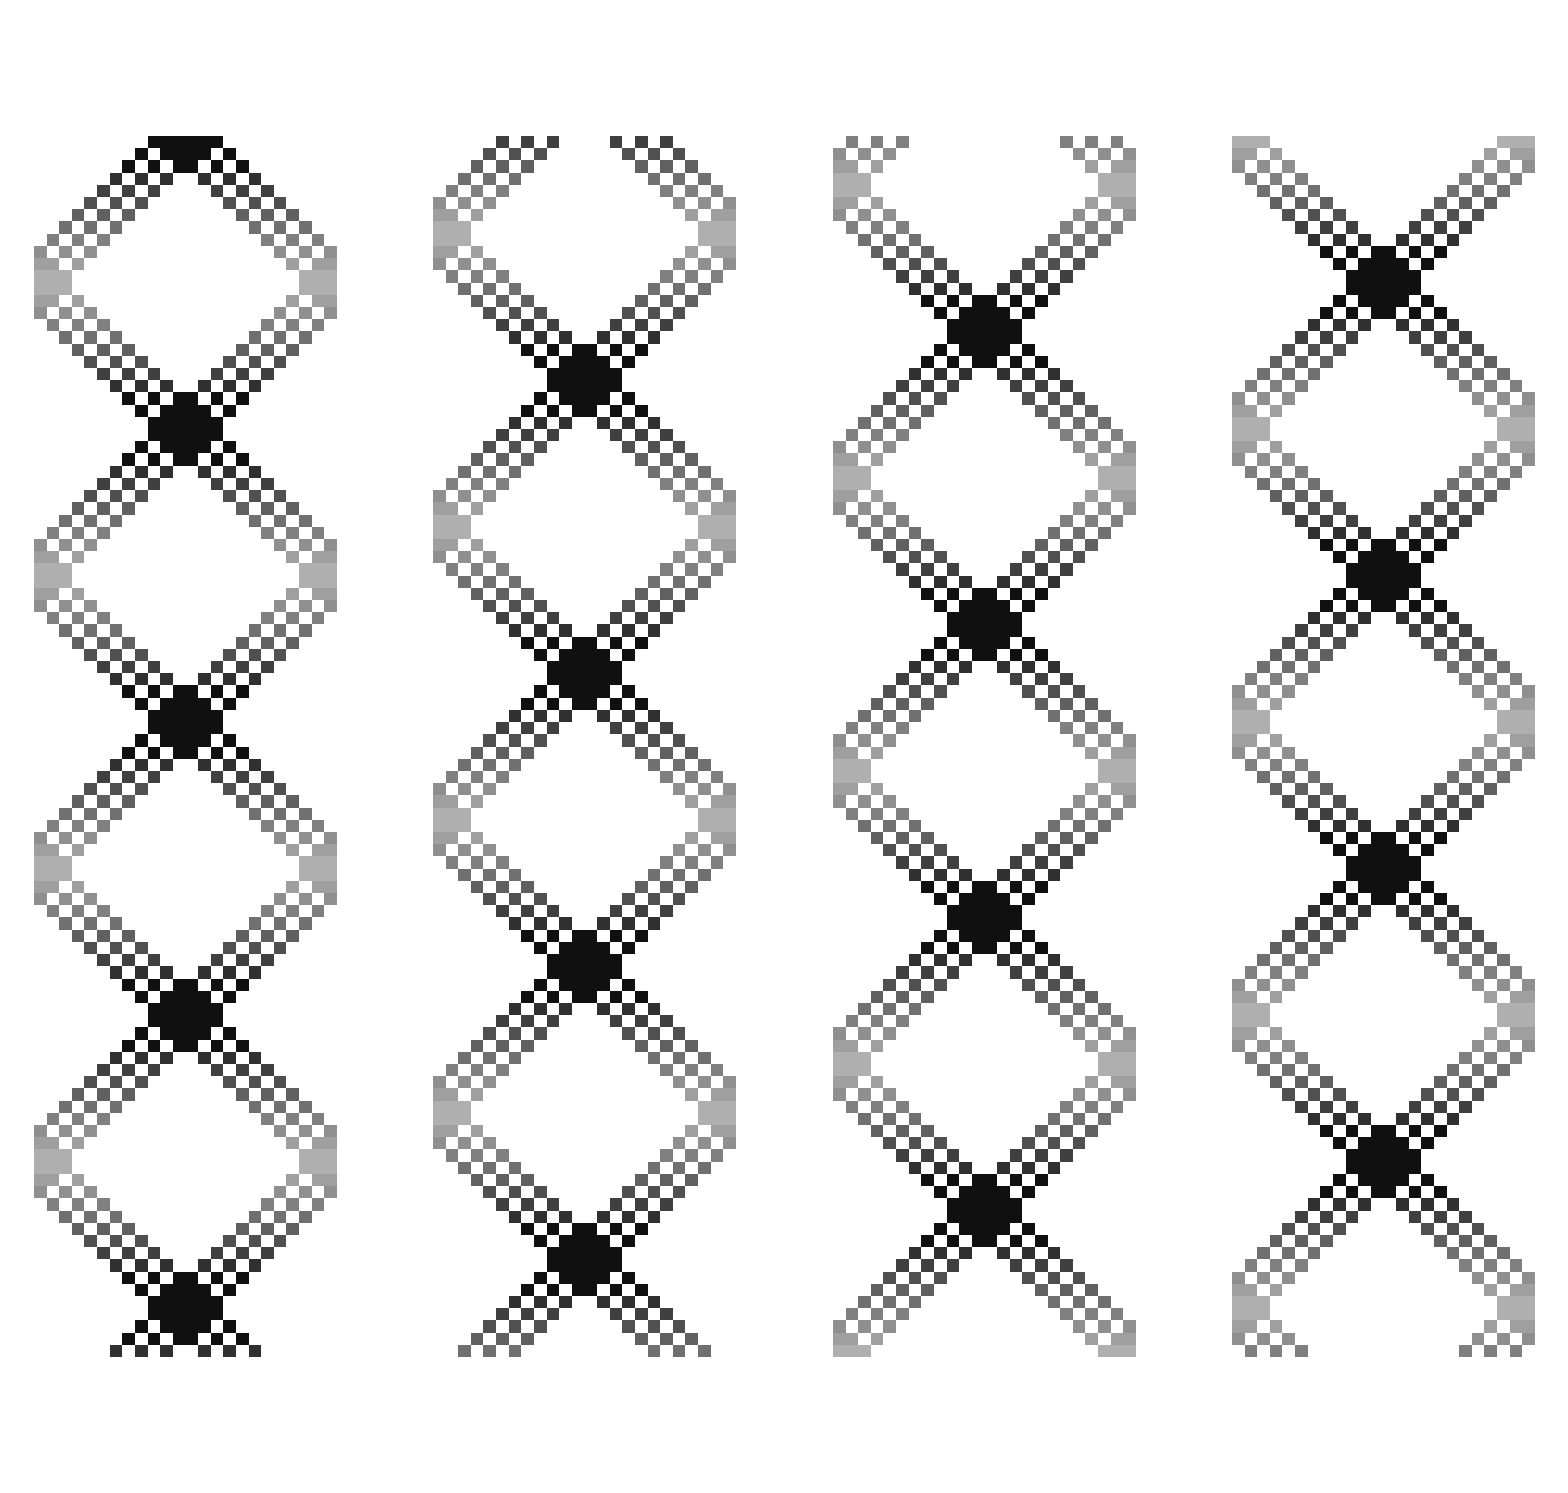
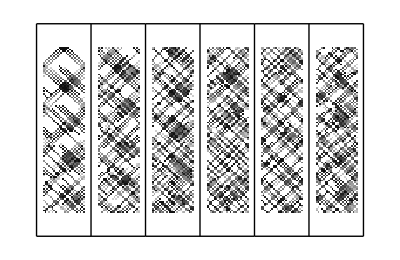

```mathematica
BCAGasEvolveList[init_,t_]:=FoldList[RotateLeft[Join@@Map[MapThread[Join,#]&,Partition[#,{2,2},{2,2},Mod[#2,2,1]]/. {{{a_,b_},{c_,d_}}/;Max[a,b,c,d]>1->{{a,b},{c,d}},{{1,0},{0,1}}->{{0,1},{1,0}},{{0,1},{1,0}}->{{1,0},{0,1}},{{a_,b_},{c_,d_}}->{{d,c},{b,a}}}],Mod[#2+1,2] {1,1}]&,init,Range[t]];

GraphicsRow[ArrayPlot[#,]&/@Partition[(First@FirstPosition[#,1,{-1}]&/@Transpose[#[[12;;]]])&/@BCAGasEvolveList[#[[1]],100 #[[2]]],100],]&/@{{CenterArray[Table[1,6,6],{24,24}],4},{CenterArray[Table[1,6,6],{24,24}]+ArrayPad[2DiamondMatrix[2],{{1,18},{1,18}}],6}}
```